```mathematica
Directory[]
ResetDirectory[];
SetDirectory["Documents/Wolfram Mathematica"] (* Set this to wherever you saved the raw data *)
rawData = ReadList["data.dat"][[1]];
rankData = Transpose[rawData[[;;, 2 ;; -2]]]; (* Last column isn't important *)
dateData = rawData[[;;, 1]];
splicedData = Table[{dateData[[n]], rankData[[m, n]]}, {n, Length@dateData}, {m, Dimensions[rankData][[1]]}] // Transpose; (* Creates a {date, data} pair for each item in each row. This is necessary for DateListPlot below. *)
titles = {"Dragon", "Rune", "Adamant", "Mithril", "Steel", "Iron"};
colours = {Red, Blend[{Darker@Cyan, Blue}, 1/5], Darker@Darker@Green, Blue, LightGray,Darker@Gray};
```

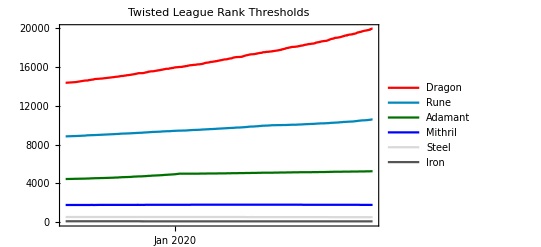

```mathematica
DateListPlot [splicedData, PlotLabel->"Twisted League Rank Thresholds",PlotStyle -> colours, PlotLegends->titles]
```